```mathematica
ClearAll["Global`*"]
```

# Data

```mathematica
(*<<D:\Work\Course_paper\diploma\Mathematica\data.txt*)
```

```mathematica
(* xmM - ионная сила [1 - концентрация мономеров лизина, 2 - потенциал на мембране]*)
{Low$40mM,Low$100mM,Middle$100mM, High$40mM, High$100mM} ={{{-5.993759750390016,-0.09636363636363637},{-5.120124804992199,-0.09313131313131318},{-4.439937597503899,-0.0850505050505051},{-3.9719188767550695,-0.05595959595959599},{-3.6099843993759744,-0.028484848484848502},{-3.2979719188767547,-0.0014141414141414232},{-2.9360374414976596,0.003434343434343401},{-2.4243369734789386,0.007474747474747467},{-2.018720748829953,0.010707070707070693}}, {{-5.993759750390016,-0.07292929292929295},{-5.120124804992199,-0.07090909090909092},{-4.433697347893915,-0.06282828282828284},{-4.433697347893915,-0.06282828282828284},{-3.9656786271450852,-0.04262626262626262},{-3.60374414976599,-0.022424242424242458},{-3.29173166926677,-0.006666666666666654},{-2.92355694227769,-0.0022222222222222365},{-2.436817472698907,0.00262626262626643},{-2.018720748829953,0.006666666666666626}}, {{-5.993759750390016,-0.07090909090909092},{-5.276131045241809,-0.07090909090909092},{-4.602184087363494,-0.06808080808080808},{-4.121684867394695,-0.05555555555555558},{-3.7659906396255844,-0.044646464646464656},{-3.44773790951638,-0.00424242424242427},{-3.092043681747269,0.016767676767676765},{-2.455538221528861,0.026868686868686847}}, {{-5.993759750390016,-.9111111111111109*10^(-1)},{-5.993759750390016,-.9111111111111109*10^(-1)},{-5.993759750390016,-.8989898989898992*10^(-1)},{-5.388455538221528,-.8707070707070708*10^(-1)},{-5.213728549141965,-.882828282828283*10^(-1)},{-4.702028081123244,-.850505050505051*10^(-1)},{-4.527301092043681,-.850505050505051*10^(-1)},{-4.234009360374415,-.7616161616161615*10^(-1)},{-4.059282371294851,-.7979797979797981*10^(-1)},{-3.6973478939157562,.6040404040404038*10^(-1)},{-3.510140405616224,.616161616161616*10^(-1)},{-3.2480499219968797,.6121212121212119*10^(-1)},{-3.0608424336973474,.6121212121212119*10^(-1)},{-2.705148205928236,.5919191919191916*10^(-1)},{-2.530421216848673,.5919191919191916*10^(-1)}},  {{-5.993759750390016,-0.07090909090909092},{-5.213728549141965,-0.07212121212121214},{-4.527301092043681,-0.07010101010101011},{-4.527301092043681,-0.07010101010101011},{-4.059282371294851,-0.06808080808080808},{-3.5163806552262087,0.04424242424242422},{-3.0608424336973474,0.04424242424242422},{-2.530421216848673,0.037373737373737365}}};
```

```mathematica
{High$10mM,Middle$10mM,Low$10mM, High$20, Middle$20,Low$20}={{{-5.392970000,-.1010000000`},{-5.213000000,-.9780000000*10^(-1)},{-5.212000000,-.9570000000*10^(-1)},{-4.710860000,-.9550000000*10^(-1)},{-4.531000000,-.9320000000*10^(-1)},{-4.530000000,-.8610000000*10^(-1)},{-4.237920000,-.8350000000*10^(-1)},{-4.058000000,-.8556000000*10^(-1)},{-4.057000000,-.8350000000*10^(-1)},{-3.878110000,-.6800000000*10^(-1)},{-3.698000000,-.7400000000*10^(-1)},{-3.670000000,-.5985000000*10^(-1)},{-3.562880000,.7150000000*10^(-1)},{-3.561000000,-.3980000000*10^(-1)},{-3.510000000,.6750000000*10^(-1)},{-3.475000000,.6336000000*10^(-1)},{-3.346000000,.7605000000*10^(-1)},{-3.198730000,.7750000000*10^(-1)},{-3.174000000,.7940000000*10^(-1)},{-3.064000000,.7800000000*10^(-1)},{-2.697240000,.8060000000*10^(-1)},{-2.558000000,.8230000000*10^(-1)},{-2.525000000,.8160000000*10^(-1)}}, {{-6,-.1029000000`},{-5.283,-.1007000000`},{-5.283,-.1026500000`},{-4.601,-.9370000000*10^(-1)},{-4.601,-.9645000000*10^(-1)},{-4.13,-.8170000000*10^(-1)},{-4.13,-.7180000000*10^(-1)},{-3.913,-.6400000000*10^(-1)},{-3.913,-.5350000000*10^(-1)},{-3.771,-.3710000000*10^(-1)},{-3.771,-.4570000000*10^(-1)},{-3.666,-.3330000000*10^(-1)},{-3.666,-.3140000000*10^(-1)},{-3.583,-.7000000000*10^(-2)},{-3.583,.3650000000*10^(-2)},{-3.515,.7300000000*10^(-2)},{-3.515,.1400000000*10^(-1)},{-3.322,.3390000000*10^(-1)},{-3.322,.3000000000*10^(-1)},{-3.035,.5320000000*10^(-1)},{-3.035,.3880000000*10^(-1)},{-2.58,.5870000000*10^(-1)},{-2.58,.5060000000*10^(-1)},{-2.336,.4850000000*10^(-1)}}, {{-6,-1.118*10^(-1)},{-5.124,-1.0435000000*10^(-1)},{-4.442,-.857000000*10^(-1)},{-3.969,-.44150000000*10^(-1)},{-3.421,-.190000000*10^(-1)},{-2.763,.1400000000*10^(-1)},{-2.368,.1880000000*10^(-1)}}, {{-5.211831629,-.627*10^(-1)},{-4.530177984,-.478*10^(-1)},{-4.290730039,-.41*10^(-2)},{-4.146910470,.1845*10^(-1)},{-3.903089987,.324*10^(-1)},{-3.480172006,.415*10^(-1)},{-2.628932138,.5035*10^(-1)}}, {{-5.392544977,-.584*10^(-1)},{-4.709965389,-.444*10^(-1)},{-4.429457060,-.120*10^(-1)},{-4.133122186,.343*10^(-1)},{-3.838631998,.396*10^(-1)},{-3.747146969,.424*10^(-1)},{-3.607303047,.444*10^(-1)}}, {{-7.00,-.620*10^(-1)},{-5.12,-.560*10^(-1)},{-4.82,-.530*10^(-1)},{-4.52,-.450*10^(-1)},{-4.34,-.390*10^(-1)},{-4.12,-.320*10^(-1)},{-3.92,-.260*10^(-1)},{-3.70,-.160*10^(-1)},{-3.56,-.139*10^(-1)},{-3.37,-.9*10^(-2)},{-3.13,-.6*10^(-2)},{-2.86,-.24*10^(-2)},{-2.4,-.5*10^(-3)}}};
```

# Model

```mathematica
(*Единицы длины-нанометры, единицы заряда - электроны*)
P=1; (*Доля заряда липида, участвующая в адсорбции*)
k=1.38*10^(-23); (*Константа больцмана*)
T=293; (*Температура*)
ϵ=80; (*Диэлектрическая проницаемость воды*)
el=1;(*Заряд электрона равен единице*)


z0=0.2; (*Толщина штерновского слоя*)
(*c0=10^-2*0.6;*) (*Концентрация электролита в шт/nm^3 (=10 mM/l)*)
ϕT=0.025; (*kT/e = 25 mV*)
adopc=0.6; (*Площадь на молекулу DOPC*)
acl=1.2; (*Площадь на молекулу кардиолипин*)
Mcl=1494; (*молярка кардиолипина*)
Mdopc=770; (*молярка DOPC*)
(*Связь минимальной толщины полимерного слоя с объёмом одного монолизина, считая, что один монолизин распластывается на половину кардиолиина (аCL = 2*adopc)*)

σ0=-P((2 el θ$e α)/acl)(*Поверхностная плотность заряда кардиолипина c поправкой на адсорбцию ионов на него*);

stot=(1/2) CLip ((adopc (1-α))/Mdopc+(acl α)/Mcl)(*Полная площадь мембраны, нормированная на объём ячейки*);

θ$e=(Sinh[-( ϕ0 /ϕT / 2)]((2 acl c0 λ)/α)); (* K1 не получаются нужные значения*);

Γ = (1/(2 K4 γ acl stot))(2α K4 stot + K4 γ acl Cc + acl - √((2 K4 α stot-K4 γ acl Cc)^2+2 K4 acl (2 α stot+γ acl)+acl^2));
θ =  (acl (1 + Cc γ K4 )+2α K4 stot θ$lim - acl √((-8 Cc γ K4^2 stot α θ$lim)/acl + (1 + Cc γ K4 + (2α K4 stot  θ$lim)/acl)^2))/(4α K4 stot);
(* σp=el((2α)/(acl G)); пока не нужно *)
(*G=stot (σp/el);*)
(*Доля площади мембраны, покрытой белком*)
σ1=σ0 + el Γ (1 - γ (1 - θ$e));
(* σ2=Min[(σ0-σ1 β K1)/(1-β) ,0];(*K3 - степень сгущения заряженного липида под лизином*) пока не нужно *)
(* 
	Clip - суммарное количество липида, образующего липосомы (в мг на мл раствора),
	α - массовая доля липида,
	acl - площадь на молекулу кардиолипина = 1.2,
	Сc - начальная концентрация мономеров полилизина в растворе,
	γ, G - геометрический параметр, указывающий на долю адсорбированных мономеров лизина,
	K4 - константа связывания ((K+)/(K-)) полимера и мембраны,
	β0, Subscript[θ, lim] - предельная доля полимерного покрытия,
	λ - Дебаевская длина - расстояние,на которое распространяется действие электрического поля отдельного заряда,
	σ1 - Плотность поверхностного заряда мембраны,
	σ0 - плотность поверхностного заряда мембраны в отсутствии полимера,
	σp - плотность заряда, вносимая полимером,
	c0 - концентрация электролита,
	Γ - плотность покрытия мономеров лизина,
	Subscript[θ, e], K1 - Коээфициент, учитывающий адсорбцию катионов на молекулах кардиолипина, константа в нашем случае
*)
	

ϕ1=2ϕT ArcSinh[σ1/(4c0 el λ)];

 Subscript[ψ, 2] = 2ϕT(θ ArcSinh[α((1/γ-1)/(2λ acl c0))] +(1 - θ) ArcSinh[(-α θ$e)/(2λ acl c0)]);

Homogeneous=ϕ1; 
Inhomogeneous = Subscript[ψ, 2];


F1[Cc_]=Homogeneous;
F[Cc_] =  Inhomogeneous;
```

# Homogeneous start conditions

```mathematica
err$Hom$High10mM = Total[(F1[10^High$10mM[[All,1]]]-High$10mM[[All,2]])^2];
su$Hom$High10mM = {λ->3,c0->10^-2*0.6,α -> 1, K1 -> 0.2, γ -> γh$10, CLip -> CL, K4-> 10^K4$h$10, ϕ0 -> High$10mM[[1, 2]]};
err$Hom$High10mM = err$Hom$High10mM/.su$Hom$High10mM;

err$Hom$Low40mM=Total[(F1[10^Low$40mM[[All,1]]]-Low$40mM[[All,2]])^2];
su$Hom$Low40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$l$40,γ->γl$40, ϕ0 -> Low$40mM[[1, 2]]};
err$Hom$Low40mM=err$Hom$Low40mM/.su$Hom$Low40mM;
err$Hom$Low100mM=Total[(F1[10^Low$100mM[[All,1]]]-Low$100mM[[All,2]])^2];
su$Hom$Low100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$l$100,  γ->γl$100, ϕ0 -> Low$100mM[[1, 2]]};
err$Hom$Low100mM=err$Hom$Low100mM/.su$Hom$Low100mM;
err$Hom$Middle100mM=Total[(F1[10^Middle$100mM[[All,1]]]-Middle$100mM[[All,2]])^2];
su$Hom$Middle100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$m$100,γ->γm$100, ϕ0 -> Middle$100mM[[1, 2]]};
err$Hom$Middle100mM=err$Hom$Middle100mM/.su$Hom$Middle100mM;
err$Hom$High40mM=Total[(F1[10^High$40mM[[All,1]]]-High$40mM[[All,2]])^2];
su$Hom$High40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$h$40, γ->γh$40, ϕ0 -> High$40mM[[1, 2]]};
err$Hom$High40mM=err$Hom$High40mM/.su$Hom$High40mM;
err$Hom$High100mM=Total[(F1[10^High$100mM[[All,1]]]-High$100mM[[All,2]])^2];
su$Hom$High100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$h$100, γ->γh$100, ϕ0 -> High$100mM[[1, 2]]};
err$Hom$High100mM=err$Hom$High100mM/.su$Hom$High100mM;

err$Hom$Middle10mM = Total[(F1[10^Middle$10mM[[All,1]]]-Middle$10mM[[All,2]])^2];
su$Hom$Middle10mM = {λ->3, c0->10^-2*0.6,α -> 1, K1 -> 0.2, CLip -> CL, K4-> 10^K4$m$10, γ->γm$10, ϕ0 -> Middle$10mM[[1, 2]]};
err$Hom$Middle10mM = err$Hom$Middle10mM/.su$Hom$Middle10mM;
err$Hom$Low10mM = Total[(F1[10^Low$10mM[[All,1]]]-Low$10mM[[All,2]])^2];
su$Hom$Low10mM = {λ->3, c0->10^-2*0.6,α -> 1,  K1 -> 0.2, CLip -> CL, K4-> 10^K4$l$10, γ->γl$10, ϕ0 -> Low$10mM[[1, 2]]};
err$Hom$Low10mM = err$Hom$Low10mM/.su$Hom$Low10mM;
(*su$Hom={CL->Sin[π/2 CL$t]^2, γl->γ0+Sin[π/2 H$l100t]^2, γm->γ0+Sin[π/2 H$m100t]^2, γh->γ0+Sin[π/2 H$h100t]^2};*)
su$Hom = {};
γ0 = 0.000001;
```

# Inhomogeneous start conditions

```mathematica
err$High10mM = Total[(F[10^High$10mM[[All,1]]]-High$10mM[[All,2]])^2];
su$High10mM = {λ->3,c0->10^-2*0.6,α -> 1, K1 -> 0.2, γ -> γh$10, CLip -> CL, K4-> 10^K4$h$10,θ$lim->θh$10, ϕ0 -> High$10mM[[1, 2]]};
err$High10mM = err$High10mM/.su$High10mM;

err$Low40mM=Total[(F[10^Low$40mM[[All,1]]]-Low$40mM[[All,2]])^2];
su$Low40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$l$40,γ->γl$40,θ$lim->θl$40, ϕ0 -> Low$40mM[[1, 2]]};
err$Low40mM=err$Low40mM/.su$Low40mM;
err$Low100mM=Total[(F[10^Low$100mM[[All,1]]]-Low$100mM[[All,2]])^2];
su$Low100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$l$100,  γ->γl$100,θ$lim->θl$100, ϕ0 -> Low$100mM[[1, 2]]};
err$Low100mM=err$Low100mM/.su$Low100mM;
err$Middle100mM=Total[(F[10^Middle$100mM[[All,1]]]-Middle$100mM[[All,2]])^2];
su$Middle100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$m$100,γ->γm$100,θ$lim->θm$100, ϕ0 -> Middle$100mM[[1, 2]]};
err$Middle100mM=err$Middle100mM/.su$Middle100mM;
err$High40mM=Total[(F[10^High$40mM[[All,1]]]-High$40mM[[All,2]])^2];
su$High40mM={λ->1.9, c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$h$40, γ->γh$40,θ$lim->θh$40, ϕ0 -> High$40mM[[1, 2]]};
err$High40mM=err$High40mM/.su$High40mM;
err$High100mM=Total[(F[10^High$100mM[[All,1]]]-High$100mM[[All,2]])^2];
su$High100mM={λ->1, c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$h$100, γ->γh$100,θ$lim->θh$100, ϕ0 -> High$100mM[[1, 2]]};
err$High100mM=err$High100mM/.su$High100mM;

err$Middle10mM = Total[(F[10^Middle$10mM[[All,1]]]-Middle$10mM[[All,2]])^2];
su$Middle10mM = {λ->3, c0->10^-2*0.6,α -> 1, K1 -> 0.2, CLip -> CL, K4-> 10^K4$m$10, γ->γm$10,θ$lim->θm$10, ϕ0 -> Middle$10mM[[1, 2]]};
err$Middle10mM = err$Middle10mM/.su$Middle10mM;
err$Low10mM = Total[(F[10^Low$10mM[[All,1]]]-Low$10mM[[All,2]])^2];
su$Low10mM = {λ->3, c0->10^-2*0.6,α -> 1,  K1 -> 0.2, CLip -> CL, K4-> 10^K4$l$10, γ->γl$10,θ$lim->θl$10, ϕ0 -> Low$10mM[[1, 2]]};
err$Low10mM = err$Low10mM/.su$Low10mM;

(*
err$High10mM=Total[(F[10^High$10mM[[All,1]]]-High$10mM[[All,2]])^2];
su$High10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,γ->γh,CLip->CL,K4->10^K4$h,θ$lim->θh, ϕ0 -> High$10mM[[1, 2]]};
err$High10mM=err$High10mM/.su$High10mM;


err$Low40mM=Total[(F[10^Low$40mM[[All,1]]]-Low$40mM[[All,2]])^2];
su$Low40mM={λ->1.9,c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl, ϕ0 -> Low$40mM[[1, 2]]};
err$Low40mM=err$Low40mM/.su$Low40mM;


err$Low100mM=Total[(F[10^Low$100mM[[All,1]]]-Low$100mM[[All,2]])^2];
su$Low100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl, ϕ0 -> Low$100mM[[1, 2]]};
err$Low100mM=err$Low100mM/.su$Low100mM;


err$Middle100mM=Total[(F[10^Middle$100mM[[All,1]]]-Middle$100mM[[All,2]])^2];
su$Middle100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$m,γ->γm,θ$lim->θm, ϕ0 -> Middle$100mM[[1, 2]]};
err$Middle100mM=err$Middle100mM/.su$Middle100mM;


err$High40mM=Total[(F[10^High$40mM[[All,1]]]-High$40mM[[All,2]])^2];
su$High40mM={λ->1.9,c0->10^-2*2.4,K1->0.25,α->1,CLip->CL,K4->10^K4$h,γ->γh,θ$lim->θh, ϕ0 -> High$40mM[[1, 2]]};
err$High40mM=err$High40mM/.su$High40mM;


err$High100mM=Total[(F[10^High$100mM[[All,1]]]-High$100mM[[All,2]])^2];
su$High100mM={λ->1,c0->10^-1*0.6,K1->0.27,α->1,CLip->CL,K4->10^K4$h,γ->γh,θ$lim->θh, ϕ0 -> High$100mM[[1, 2]]};
err$High100mM=err$High100mM/.su$High100mM;


err$Middle10mM=Total[(F[10^Middle$10mM[[All,1]]]-Middle$10mM[[All,2]])^2];
su$Middle10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,CLip->CL,K4->10^K4$m,γ->γm,θ$lim->θm, ϕ0 -> Middle$10mM[[1, 2]]};
err$Middle10mM=err$Middle10mM/.su$Middle10mM;


err$Low10mM=Total[(F[10^Low$10mM[[All,1]]]-Low$10mM[[All,2]])^2];
su$Low10mM={λ->3,c0->10^-2*0.6,α->1,K1->0.2,CLip->CL,K4->10^K4$l,γ->γl,θ$lim->θl, ϕ0 -> Low$10mM[[1, 2]]};
err$Low10mM=err$Low10mM/.su$Low10mM;

(*su={CL->Sin[π/2 CL$t]^2, γl->γ0+Sin[π/2 H$l100t]^2, γm->γ0+Sin[π/2 H$m100t]^2, γh->γ0+Sin[π/2 H$h100t]^2,
θl->Sin[π/2 H$l100t]^2, θm->Sin[π/2 H$m100t]^2, θh->Sin[π/2 H$h100t]^2};*)*)
su = {};
```

# Homogeneous minimize

### Defining variables and constraints to minimize

```mathematica
(* Нужна при построенни графиков для обратной подстановки К4 (Костыль, нужно сделать выбор переменных перед установкой начальных условий)*)
K4$replace={};
(* Определение функции общей ошибки *)
errf$Hom=err$Hom$Low100mM+err$Hom$Low40mM+err$Hom$Low10mM+ err$Hom$Middle100mM+err$Hom$Middle10mM+err$Hom$High100mM+err$Hom$High40mM+ err$Hom$High10mM/.su;

min$Hom$start={CL->0.48374,
γh$10->0.791923,γh$40->0.791923,γh$100->0.791923,
γm$10->0.399189,γm$100->0.399189,
γl$10->0.278049, γl$40->0.278049, γl$100->0.278049, 
K4$h$10->14.075, K4$h$40->14.075, K4$h$100->14.075,
K4$m$10->8.67786, K4$m$100->8.67786,
K4$l$100->26.9251,K4$l$10->26.9251, K4$l$40->26.9251};

(**)
limits = 0≤ CL≤1 &&
 γ0<γl$10<1 && γ0<γl$40<1 && γ0<γl$100<1&&
 γ0<γm$10<1 && γ0<γm$100<1 &&
 γ0<γh$10<1 && γ0<γh$40<1  && γ0<γh$100<1;

(* !!! Комментировать блоки ниже при необходимости провести минимизацию по другим параметрам*)
(* Переход к 3 гаммам (в зависимости от ионной силы)*)
If[True,
errf$Hom = errf$Hom/.{
γh$10->γ$10,γh$40->γ$40,γh$100->γ$100,
γm$10->γ$10,γm$100->γ$100,
γl$10->γ$10, γl$40->γ$40, γl$100->γ$100};

limits =0≤ CL≤1 && γ0<γ$10<1&&γ0<γ$40<1&&γ0<γ$100 < 1;]

(*-----------------------------------------------------------------------------------------------*)
(*Переход к 3 гаммам (в зависимости от длины полимера)*)
If[False,
errf$Hom = errf$Hom/.{
γh$10->γh,γh$40->γh,γh$100->γh,
γm$10->γm,γm$100->γm,
γl$10->γl, γl$40->γl, γl$100->γl};

min$Hom$start=Join[min$Hom$start,{γl->0.993796,γm->0.952403,γh->0.914842}];
limits =0≤ CL≤1 && γ0<γl<1&&γ0<γm<1&&γ0<γh < 1;]

(*-----------------------------------------------------------------------------------------------*)(*Переход к 3 константам связывания (в зависимости от длины полимера)*)
If[True,
K4$replace={
K4$h$10->K4$h,K4$h$40->K4$h,K4$h$100->K4$h,
K4$m$10->K4$m,K4$m$100->K4$m,
K4$l$10->K4$l,K4$l$40->K4$l,K4$l$100->K4$l};
errf$Hom=errf$Hom/.K4$replace;
limits=limits/.K4$replace;]

(*-----------------------------------------------------------------------------------------------*)
(* Переход к 3 константам связывания (в зависимости от ионной силы)*) 
If[False,
K4$replace = {
K4$h$10->K4$10, K4$h$40->K4$40, K4$h$100->K4$100,
K4$m$10->K4$10, K4$m$100->K4$100,
K4$l$10->K4$10,K4$l$40->K4$40, K4$l$100->K4$100};
errf$Hom = errf$Hom/.K4$replace;
min$Hom$start=Join[min$Hom$start,{CL->0.48374}];]

(**)
```

### Minimize

```mathematica
vars$Hom=Variables[Level[errf$Hom,{-1}]]

(*vars$Hom=Table[{var$val[[1]],0.9*Abs[var$val[[2]]],1.1*Abs[var$val[[2]]]},{var$val,min$Hom$start}];*)
min$Hom$fin=NMinimize[{errf$Hom,  limits},vars$Hom, MaxIterations->1000]
su$Hom$min=Join[su$Hom/.min$Hom$fin[[2]],min$Hom$fin[[2]]]
```

{CL,K4$h,K4$l,K4$m,γ$10,γ$100,γ$40}

{0.045849,{CL→0.469771,K4$h→33.0842,K4$l→7.7335,K4$m→15.7239,γ$10→0.950144,γ$100→0.948153,γ$40→0.898956}}

{CL→0.469771,K4$h→33.0842,K4$l→7.7335,K4$m→15.7239,γ$10→0.950144,γ$100→0.948153,γ$40→0.898956}

### Middle Results

Results:
{0.0356445,{
CL→0.48374,			
γl→0.993796,			γm→0.952403,			γh→0.914842,
K4$h→14.075,
K4$m→8.67786,
K4$l→26.9251}}

Result with 3 K4 (by length) and 3 gamma(by ionic force) (good):
{0.045849,{
CL→0.469771,
K4$h→33.0842,		K4$m→15.7239,		K4$l→7.7335,
γ$10→0.950144,		γ$40→0.898956,		γ$100→0.948153}}

Results with different K4:
{0.0359103,{
CL→0.485329,			
γl→0.993783,			γm→0.954718,			γh→0.914434,
K4$h$10→15.7634,		K4$h$40→42.766,		K4$h$100→26.7723,
K4$m$10→8.89956,							K4$m$100→27.1343,
K4$l$10→77.1972,		K4$l$40→39.5823,		K4$l$100→113.889}}

Results with different K4 and gamma:
{0.0532212,{
CL→0.470304,
γh$10→0.932256,		γh$40→0.812495,		γh$100→0.870496,
γm$10→0.95413,							γm$100→0.96526,
γl$10→0.994747,		γl$40→0.987278,		γl$100→0.934797,

K4$h$10→100.468,		K4$h$40→16.9145,		K4$h$100→30.2757,
K4$m$10→8.66453,							K4$m$100→30.4953,
K4$l$10→34.3702,		K4$l$40→47.4013,		K4$l$100→-16.445}}

### Errors

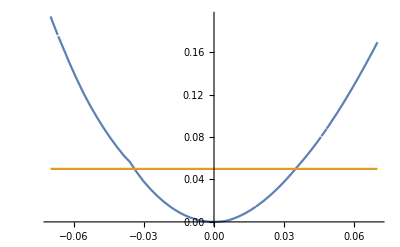
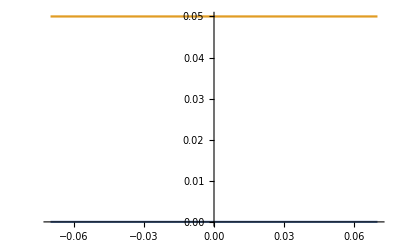
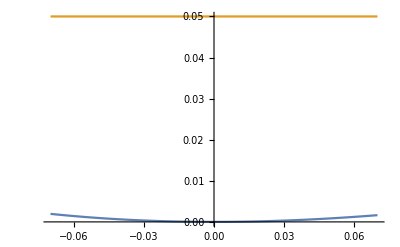
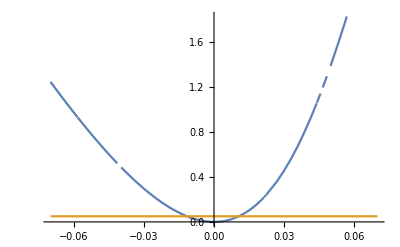
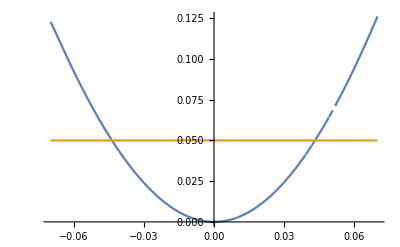
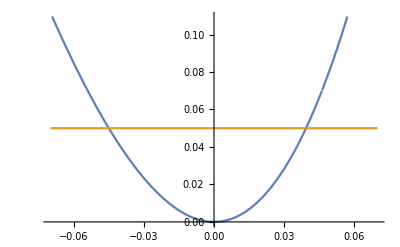
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plts={};

For[i=1,i<=Length[vars$Hom],i++,
result = su$Hom$min/.(vars[[i]]->x_)->(vars$Hom[[i]]->((vars$Hom[[i]]/.su$Hom$min)+w));
ss=0.07;
Fcurr= ((errf$Hom/.result)-(errf$Hom/.su$Hom$min))/(errf$Hom/.su$Hom$min);

AppendTo[plts, Plot[{Fcurr,0.05},{w,-ss,ss}, PlotLegends->vars$Hom[[i]]]];
]

plts
```

# Inhomogeneous minimize

### Defining variables and constraints to minimize

```mathematica
(* Нужна при построенни графиков для обратной подстановки К4 и γ *)
K4$replace={};
γ$replace = {};
(* Определение функции общей ошибки *)
errf=err$Low100mM+err$Low40mM+err$Low10mM+err$Middle100mM+err$Middle10mM+err$High100mM+err$High40mM+err$High10mM/.su;

min$start={CL->0.48374,
γh$10->0.791923,γh$40->0.791923,γh$100->0.791923,
γm$10->0.399189,γm$100->0.399189,
γl$10->0.278049, γl$40->0.278049, γl$100->0.278049, 

K4$h$10->14.075, K4$h$40->14.075, K4$h$100->14.075,
K4$m$10->8.67786, K4$m$100->8.67786,
K4$l$100->26.9251,K4$l$10->26.9251, K4$l$40->26.9251,

θh$10->1.,θh$40->0.8193335204807461,θh$100->0.6337875706309387,
θm$10->0.9011637078054321,θm$100->0.5460206189179563,
θl$10->0.6792480065656037,θl$40->0.5574179633372702,θl$100->0.4299314916173969};

(* (Решено пока костылем сверху) Не работает из-за того, что в имите должны быть только те переменные, которые есть в уравнениях*)
limits = 0≤ CL≤1 &&
 γ0<γl$10<1 && γ0<γl$40<1 && γ0<γl$100<1&&
 γ0<γm$10<1 && γ0<γm$100<1 &&
 γ0<γh$10<1 && γ0<γh$40<1  && γ0<γh$100<1&&

γ0<θh$10<1&&γ0<θh$40<1&&γ0<θh$100<1&&
γ0<θm$10<1 &&γ0<θm$100<1&&
γ0<θl$10<1&&γ0<θl$40<1&&γ0<θl$100<1&&

K4$h$10 >0 &&K4$h$40 >0 &&K4$h$100 >0 &&
K4$m$10 >0 &&K4$m$100 >0 &&
K4$l$10 >0 &&K4$l$40 >0 &&K4$l$100 >0 ;

(* !!! Комментировать блоки ниже при необходимости провести минимизацию по другим параметрам*)
(*-----------------------------------------------------------------------------------------------*)
(* Переход к 3 гаммам (в зависимости от длины полимера)*)
If[False,
errf$Hom = errf$Hom/.{
γh$10->γh,γh$40->γh,γh$100->γh,
γm$10->γm,γm$100->γm,
γl$10->γl, γl$40->γl, γl$100->γl};
min$start=Join[min$Hom$start,{γl->0.993796,γm->0.952403,γh->0.914842}];
limits =0≤ CL≤1 && γ0<γl<1&&γ0<γm<1&&γ0<γh<1;]


(* Переход к 3 гаммам (в зависимости от ионной силы)*)
If[False,
γ$replace = {
γh$10->γ$10,γh$40->γ$40,γh$100->γ$100,
γm$10->γ$10,γm$100->γ$100,
γl$10->γ$10, γl$40->γ$40, γl$100->γ$100};
errf = errf/.γ$replace;
(*min$Hom$start=Join[min$Hom$start,{γl->0.993796,γm->0.952403,γh->0.914842}];*)
limits =limits/.γ$replace;]

(*-----------------------------------------------------------------------------------------------*)
(* Переход к 1 константе связывания (в зависимости от длины полимера)*)
If[False,
K4$replace = {
K4$h$10->K4, K4$h$40->K4, K4$h$100->K4,
K4$m$10->K4, K4$m$100->K4,
K4$l$10->K4,K4$l$40->K4, K4$l$100->K4};
errf= errf/.K4$replace;
limits = limits/.K4$replace;]

(* Переход к 3 константам связывания (в зависимости от длины полимера)*)
If[True,
K4$replace = {
K4$h$10->K4$h, K4$h$40->K4$h, K4$h$100->K4$h,
K4$m$10->K4$m, K4$m$100->K4$m,
K4$l$10->K4$l,K4$l$40->K4$l, K4$l$100->K4$l};
errf= errf/.K4$replace;
limits = limits/.K4$replace;]


(* Переход к 3 константам связывания (в зависимости от ионной силы)*)
If[False,
K4$replace = {
K4$h$10->K4$10, K4$h$40->K4$40, K4$h$100->K4$100,
K4$m$10->K4$10, K4$m$100->K4$100,
K4$l$10->K4$10,K4$l$40->K4$40, K4$l$100->K4$100};
errf= errf/.K4$replace;
limits = limits/.K4$replace;]

(*-----------------------------------------------------------------------------------------------*)
(* Переход к 3 теттам связывания (в зависимости от ионной силы)*)
If[True,
θ$replace = {
θh$10->θh$10,θh$40->θh$40,θh$100->θh$100,
θm$10->θh$10,θm$100->θh$100,
θl$10->θh$10,θl$40->θh$40,θl$100->θh$100};
errf = errf/.θ$replace;
limits = limits/.θ$replace;]
```

### Minimize

```mathematica
vars=Variables[Level[errf,{-1}]]

(*vars=Table[{var$val[[1]],0.9*Abs[var$val[[2]]],1.1*Abs[var$val[[2]]]},{var$val,min$start}];
0≤CL≤1&&γ0<γl<1&&γ0<γm<1&&γ0<γh<1&&γ0<θl<1&&γ0<θm<1 &&γ0<θh<1*)
min$fin=NMinimize[{errf, limits},vars,MaxIterations->1000]
su$min=Join[su/.min$fin[[2]],min$fin[[2]]]
```

{CL,K4$h,K4$l,K4$m,γh$10,γh$100,γh$40,γl$10,γl$100,γl$40,γm$10,γm$100,θh$10,θh$100,θh$40}

{0.0296361,{CL→0.54647,K4$h→13.2731,K4$l→4.60046,K4$m→13.7536,γh$10→0.915772,γh$100→0.453329,γh$40→0.7373,γl$10→0.983297,γl$100→0.6803,γl$40→0.924926,γm$10→0.960561,γm$100→0.343194,θh$10→1.,θh$100→0.453773,θh$40→0.812051}}

{CL→0.54647,K4$h→13.2731,K4$l→4.60046,K4$m→13.7536,γh$10→0.915772,γh$100→0.453329,γh$40→0.7373,γl$10→0.983297,γl$100→0.6803,γl$40→0.924926,γm$10→0.960561,γm$100→0.343194,θh$10→1.,θh$100→0.453773,θh$40→0.812051}

### Middle Results

Results:
{0.0289636,{
CL→0.294034,
γl→0.980648,			γm→0.223942,			γh→0.253916,
θl→0.979419,			θm→0.425361,			θh→0.512033,
K4$h→19.8072,
K4$m→5.29912,
K4$l→4.28867}}

Result with  8 gamma, 8 theta, 3 K4 (depends on ionic force) (good approximation):
{0.0268452,{
CL→0.500467,
K4$10→6.18253,
K4$40→13.1782,
K4$100→6.0333,

γh$10→0.450665,		γh$40→0.741891,		γh$100→0.730233,
γm$10→0.96479,							γm$100→0.963946,
γl$10→0.789643,		γl$40→0.364441,		γl$100→0.997811,

θh$10→0.601782,		θh$40→0.818839,		θh$100→0.73312,
θm$10→1.,								θm$100→1.,
θl$10→0.490957,		θl$40→0.37631,		θl$100→0.992699}}

Result with  all variables:
{0.0214165,{
CL→0.354636,
K4$h$10→7.84156,		K4$h$40→9.52453,		K4$h$100→8.61215,
K4$l$10→4.44687,		K4$l$40→4.69061,		K4$l$100→4.21131,
K4$m$10→5.4096,							K4$m$100→3.86541,

γh$10→0.28117,		γh$40→0.741894,		γh$100→0.889218,
γl$10→0.791885,		γl$40→0.430602,		γl$100→0.839228,
γm$10→0.273206,							γm$100→0.903863,

θh$10→0.532049,		θh$40→0.820376,		θh$100→1.,
θm$10→0.449327,							θm$100→1.,
θl$10→0.533536,		θl$40→0.416153,		θl$100→0.611206}}

Results with

### Errors

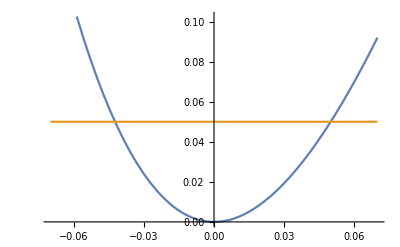
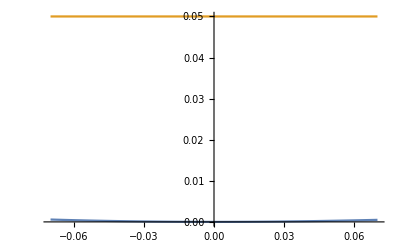
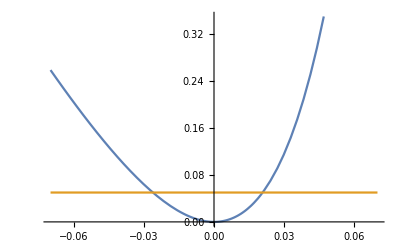
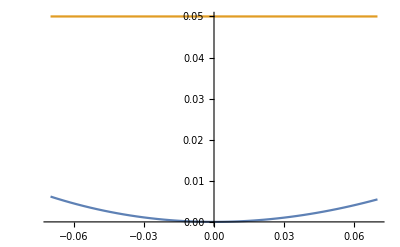
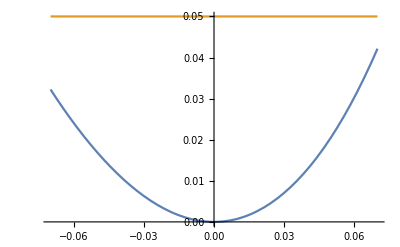
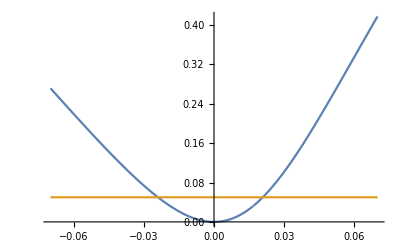
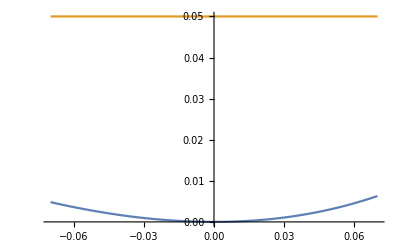
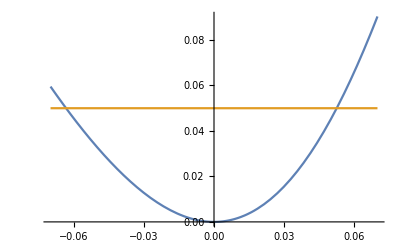
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plts={};

For[i=1,i<=Length[vars],i++,
result = su$min/.(vars[[i]]->x_)->(vars[[i]]->((vars[[i]]/.su$min)+w));
ss=0.07;
Fcurr= ((errf/.result)-(errf/.su$min))/(errf/.su$min);

AppendTo[plts, Plot[{Fcurr,0.05},{w,-ss,ss}, PlotLegends->vars[[i]]]];
]

plts
```

# Plot

## Homogeneous

### Defenition

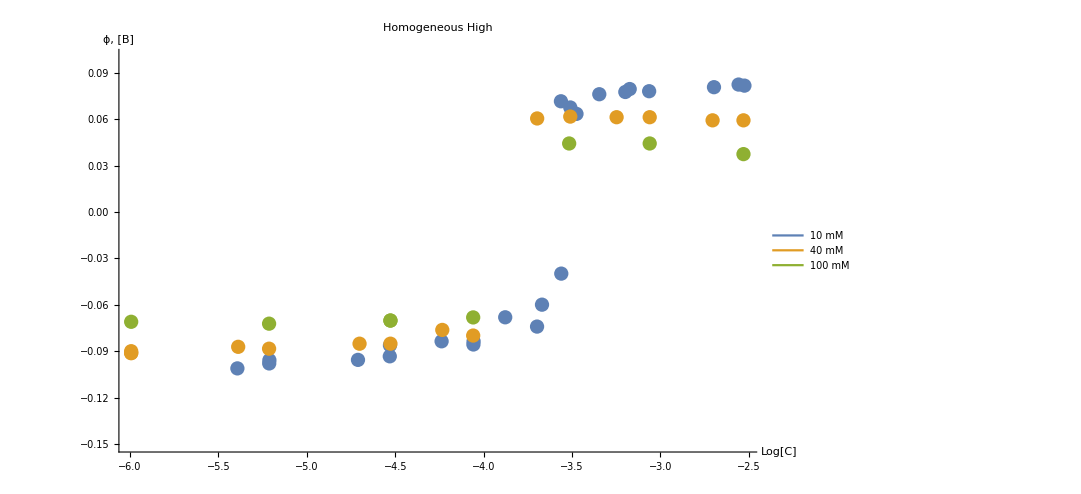

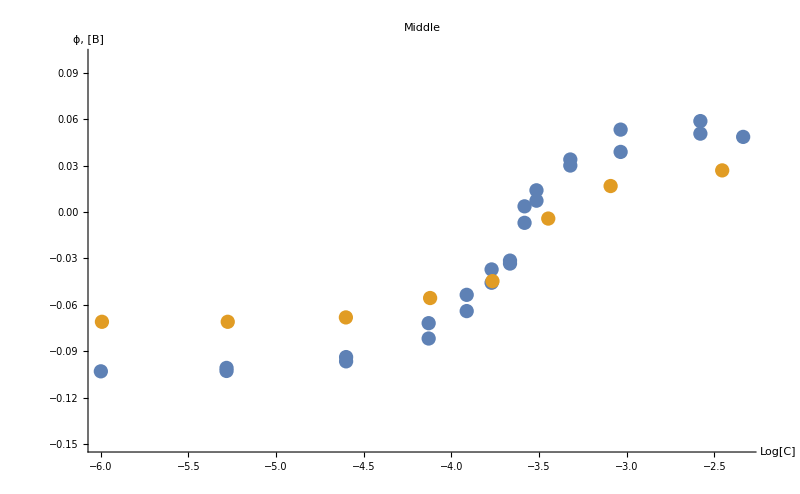

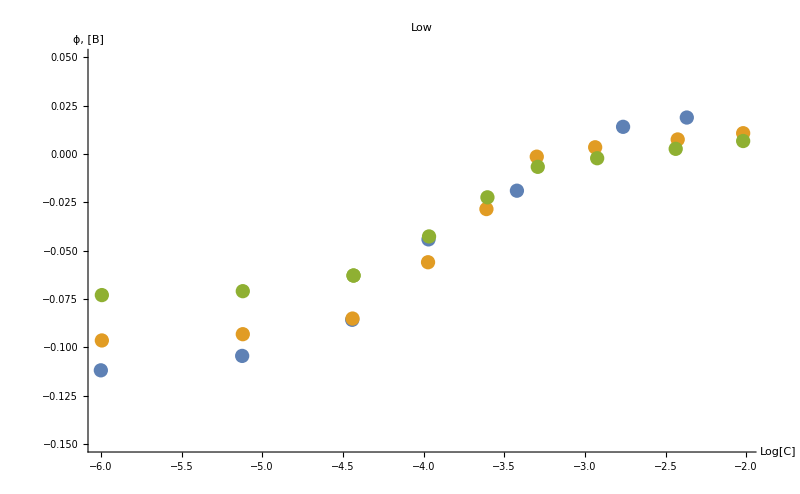

```mathematica
cmin$100=Min[Low$40mM[[All,1]]];cmax$100=Max[Low$40mM[[All,1]]];
pl1=Show[Plot[Evaluate[{F1[10^cc]/.su$Hom$High10mM,F1[10^cc]/.su$Hom$High40mM,F1[10^cc]/.su$Hom$High100mM}/.K4$replace/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2,PlotLabel->"Homogeneous\nHigh",PlotLegends->Placed[{"10 mM","40 mM", "100 mM"}, {0.2, 0.75}], ImageSize->{800,500}], 
ListPlot[{High$10mM,High$40mM, High$100mM },PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl2=Show[Plot[Evaluate[{ F1[10^cc]/.su$Hom$Middle10mM,F1[10^cc]/.su$Hom$Middle100mM}/.K4$replace/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2, ImageSize->{800,500},PlotLabel->"Middle"], 
ListPlot[{ Middle$10mM,Middle$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl3=Show[Plot[Evaluate[{F1[10^cc]/.su$Hom$Low10mM,F1[10^cc]/.su$Hom$Low40mM,F1[10^cc]/.su$Hom$Low100mM}/.K4$replace/.su$Hom$min],{cc,cmin$100,cmax$100},PlotStyle->colors2, ImageSize->{800,500},PlotLabel->"Low"], ListPlot[{Low$10mM,Low$40mM,Low$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.05},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
```

### Show

```mathematica
pl1
pl2
pl3
```

-Graphics-

-Graphics-

-Graphics-

## Inhomogeneous

### Defenition

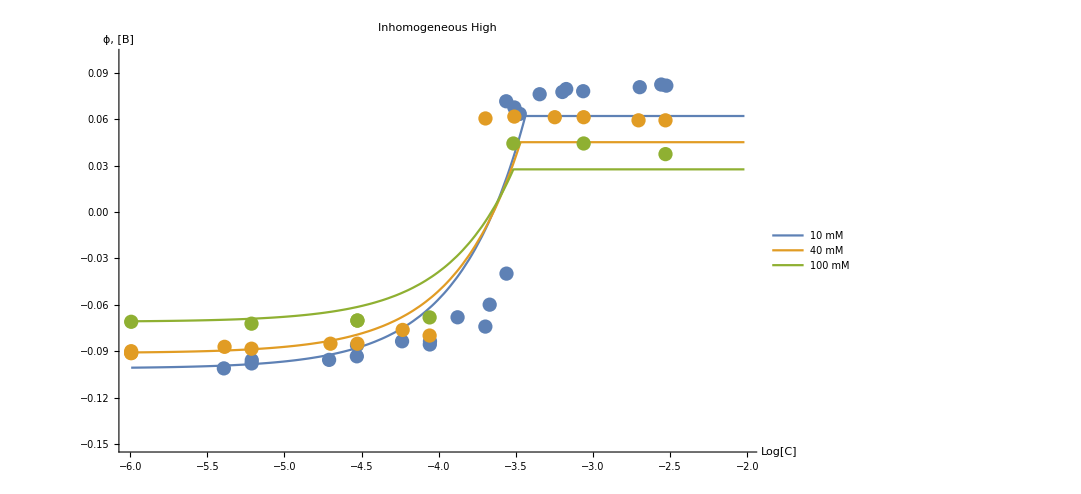

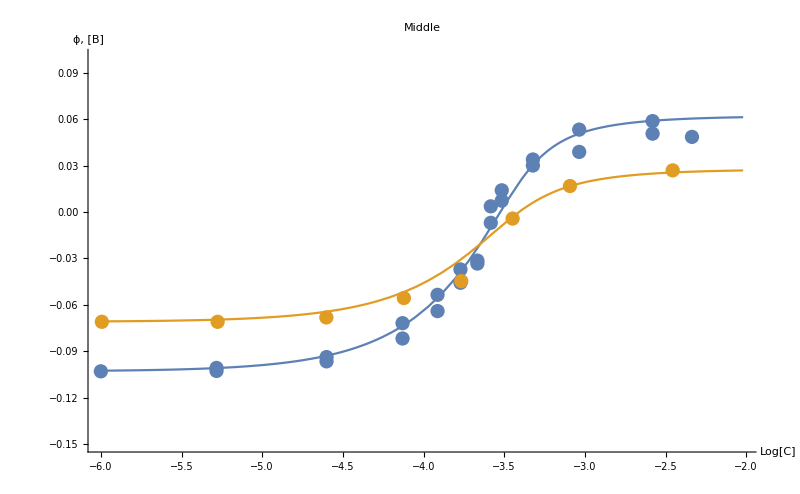

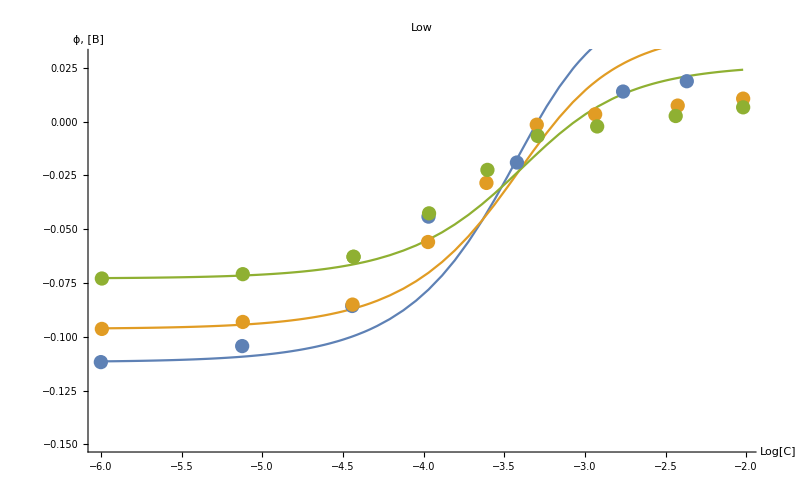

```mathematica
cmin$100=Min[Low$40mM[[All,1]]];cmax$100=Max[Low$40mM[[All,1]]];

pl4=Show[
 Plot[Evaluate[{F[10^cc]/.su$High10mM,F[10^cc]/.su$High40mM,F[10^cc]/.su$High100mM}
/.K4$replace/.γ$replace/.θ$replace/.su$min],
{cc,cmin$100,cmax$100},PlotLabel->"Inhomogeneous\nHigh",PlotLegends->Placed[{"10 mM","40 mM", "100 mM"}, {0.2, 0.75}], ImageSize->{800,500}],ListPlot[{High$10mM,High$40mM, High$100mM },PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl5=Show[ Plot[Evaluate[{ F[10^cc]/.su$Middle10mM,F[10^cc]/.su$Middle100mM}
/.K4$replace/.γ$replace/.θ$replace/.su$min],
{cc,cmin$100,cmax$100},PlotLabel->"Middle", ImageSize->{800,500}],
ListPlot[{ Middle$10mM,Middle$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.1},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]

pl6=Show[
 Plot[Evaluate[{F[10^cc]/.su$Low10mM,F[10^cc]/.su$Low40mM,F[10^cc]/.su$Low100mM}
/.K4$replace/.γ$replace/.θ$replace/.su$min],
{cc,cmin$100,cmax$100},PlotLabel->"Low", ImageSize->{800,500}],
ListPlot[{Low$10mM,Low$40mM,Low$100mM},PlotStyle->colors2],PlotRange->{-0.15,0.03},AxesLabel->{"Log[C]","ϕ, [В]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
```

### Show

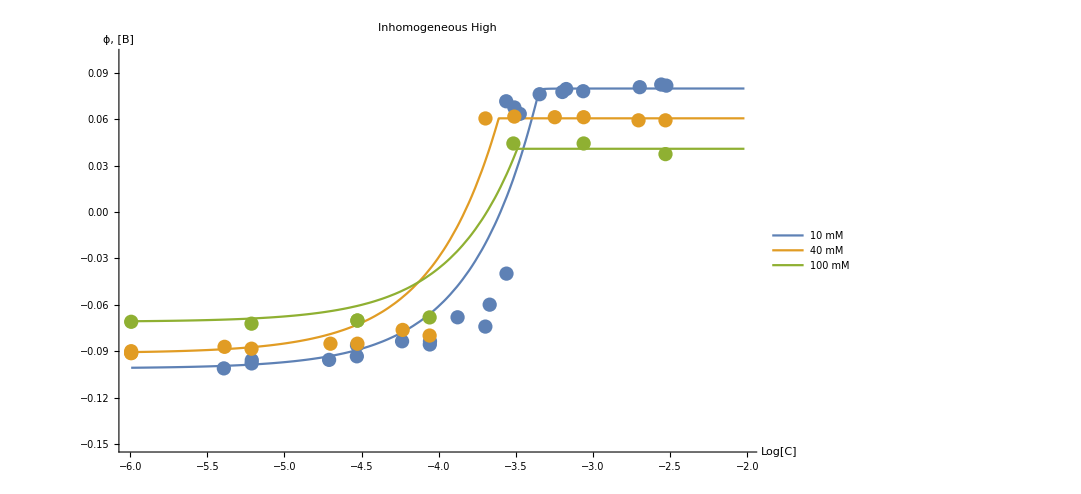

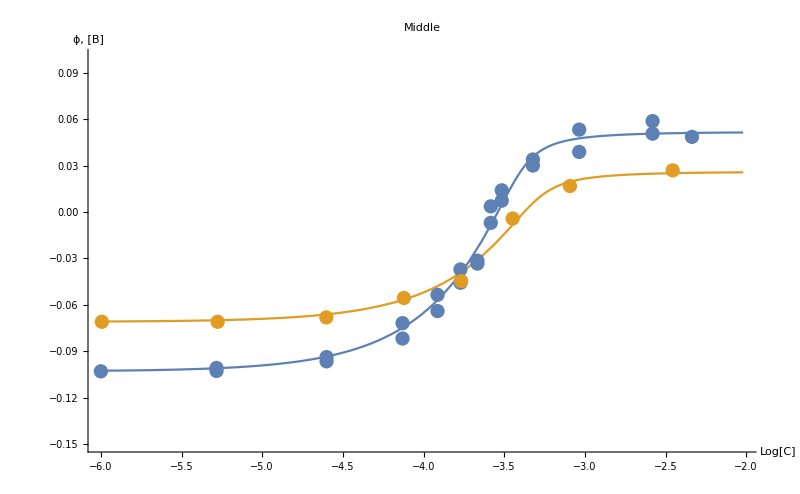

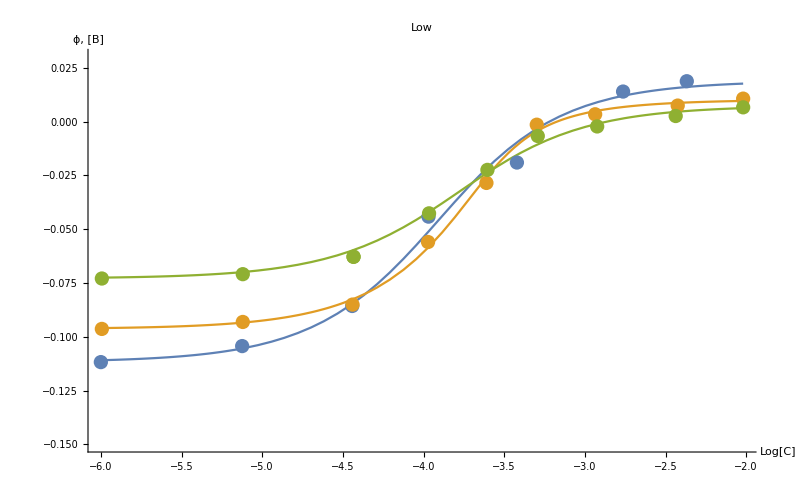

```mathematica
pl4
pl5
pl6
```

# Results (θ)

```mathematica
(* Inhomogenous Result{CL->0.47022720996122674,γl->0.8312631776412122,γm->0.9448140526641365,γh->0.4948318804417655,θl->0.5871130558286928,θm->1.,θh->0.6178470405941097,K4$h->24.63279374542971,K4$l->4.288737210950081,K4$m->4.521099348710936};*)
InhomogenousResult={CL->0.47022720996122674,γl->0.8312631776412122,γm->0.9448140526641365,γh->0.4948318804417655,θl->0.5871130558286928,θm->1.,θh->0.6178470405941097,K4$h->24.63279374542971,K4$l->4.288737210950081,K4$m->4.521099348710936};


G[Cc_] =1/(4α K4 stot)(acl (1 + Cc γ K4 )+2α K4 stot θ$lim - acl √((-8 Cc γ K4^2 stot α θ$lim)/acl + (1 + Cc γ K4 + (2α K4 stot  θ$lim)/acl)^2))*100;
resultHigh = {K4$h-> 10^24.63279374542971, θ$lim -> 0.6178470405941097,  γ -> 0.4948318804417655, CL->0.47022720996122674};
G[10^High$10mM[[All,1]]]/.su$High10mM/.InhomogenousResult



Show[ListPlot[
{G[10^High$10mM[[All,1]]]/.su$High10mM/.InhomogenousResult,
G[10^High$40mM[[All,1]]]/.su$High40mM/.InhomogenousResult,
G[10^High$100mM[[All,1]]]/.su$High100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
Show[ListPlot[
{G[10^Middle$10mM[[All,1]]]/.su$Middle10mM/.InhomogenousResult,
G[10^Middle$100mM[[All,1]]]/.su$Middle100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
Show[ListPlot[
{G[10^Low$10mM[[All,1]]]/.su$Low10mM/.InhomogenousResult,
G[10^Low$40mM[[All,1]]]/.su$Low40mM/.InhomogenousResult,
G[10^Low$100mM[[All,1]]]/.su$Low100mM/.InhomogenousResult}, PlotStyle->colors2],AxesLabel->{"Log[C]","θ, [%]"},LabelStyle->Directive[Black,Bold,FontSize->15],AxesStyle->Thickness[0.008]]
```

{132383. 10^-K4$h$10 (1.2 (1+4.04604×10^-6 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-5.09386×10^-9 10^(2 K4$h$10) γh$10 θh$10+(1+4.04604×10^-6 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+6.1235×10^-6 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-7.70934×10^-9 10^(2 K4$h$10) γh$10 θh$10+(1+6.1235×10^-6 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+6.13762×10^-6 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-7.72711×10^-9 10^(2 K4$h$10) γh$10 θh$10+(1+6.13762×10^-6 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000194599 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-2.44995×10^-8 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000194599 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000294442 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.70695×10^-8 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000294442 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000295121 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.7155×10^-8 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000295121 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000578203 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-7.27943×10^-8 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000578203 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000874984 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-1.10158×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000874984 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.0000877001 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-1.10412×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.0000877001 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000132401 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-1.66689×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000132401 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000200447 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-2.52358×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000200447 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000213796 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-2.69164×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000213796 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000273602 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.44459×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000273602 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000274789 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.45953×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000274789 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.00030903 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.89061×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.00030903 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000334965 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-4.21713×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000334965 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000450817 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-5.67567×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000450817 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000632805 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-7.96686×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000632805 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000669885 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-8.43368×10^-7 10^(2 K4$h$10) γh$10 θh$10+(1+0.000669885 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.000862979 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-1.08647×10^-6 10^(2 K4$h$10) γh$10 θh$10+(1+0.000862979 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.00200798 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-2.528×10^-6 10^(2 K4$h$10) γh$10 θh$10+(1+0.00200798 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.00276694 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.48351×10^-6 10^(2 K4$h$10) γh$10 θh$10+(1+0.00276694 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2)),132383. 10^-K4$h$10 (1.2 (1+0.00298538 10^K4$h$10 γh$10)+0.000377693 10^K4$h$10 θh$10-1.2 √(-3.75852×10^-6 10^(2 K4$h$10) γh$10 θh$10+(1+0.00298538 10^K4$h$10 γh$10+0.000314744 10^K4$h$10 θh$10)^2))}

-Graphics-

-Graphics-

-Graphics-